```mathematica
Solve[0.5*g*t^2-vz*t+delta==0,t]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→(vz-1. √(-2. delta g+vz^2))/g},{t→(vz+√(-2. delta g+vz^2))/g}}

```mathematica
vz = v * Cos[alpha];
vh = v * Sin[alpha];
t = d/vh;
Simplify[Solve[(vz+√(-2* Δ g+vz^2))/g==t,alpha]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{alpha→-ArcCos[-(√((2 v^4 Δ^2-√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→ArcCos[-(√((2 v^4 Δ^2-√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→-ArcCos[(√((2 v^4 Δ^2-√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→ArcCos[(√((2 v^4 Δ^2-√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→-ArcCos[-(√((2 v^4 Δ^2+√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→ArcCos[-(√((2 v^4 Δ^2+√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→-ArcCos[(√((2 v^4 Δ^2+√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]},{alpha→ArcCos[(√((2 v^4 Δ^2+√(d^4 v^4 (-d^2 g^2+v^4-2 g v^2 Δ))+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]}}

```mathematica
FullSimplify[(√((2 v^4 Δ^2+d^2 v^2 √(-d^2 g^2+v^4-2 g v^2 Δ)+d^2 (v^4+g v^2 Δ))/(v^4 (d^2+Δ^2))))/(√2)]
FullSimplify[√((2 v^2 Δ^2+d^2 (v^2+g Δ+√(v^4-g (d^2 g+2 v^2 Δ))))/(2*v^2 (d^2+Δ^2)))]
Cos(angle)=√((2 v^2 Δ^2+d^2 (v^2+g Δ+√(v^4-g (d^2 g+2 v^2 Δ))))/(2*v^2 (d^2+Δ^2)))
```

(√((2 v^2 Δ^2+d^2 (v^2+g Δ+√(v^4-g (d^2 g+2 v^2 Δ))))/(v^2 (d^2+Δ^2))))/(√2)

(√((2 v^2 Δ^2+d^2 (v^2+g Δ+√(v^4-g (d^2 g+2 v^2 Δ))))/(v^2 (d^2+Δ^2))))/(√2)

15

100

-9.8

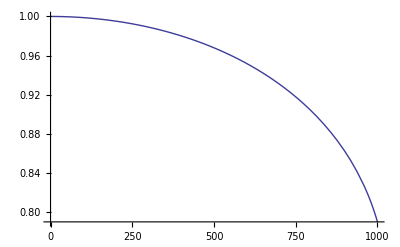

```mathematica
Δ = 15
v = 100
g = -9.8
Plot[√((2 v^2 Δ^2+d^2 (v^2+g Δ+√(v^4-g (d^2 g+2 v^2 Δ))))/(2*v^2 (d^2+Δ^2))), {d, 0, 1000}]
```

(√((100000000 distance^2+10000 √(distance^4 (100000000-100 distance^2)))/distance^2))/(10000 √2)

√(1-(100000000 distance^2+10000 √(distance^4 (100000000-100 distance^2)))/(200000000 distance^2))

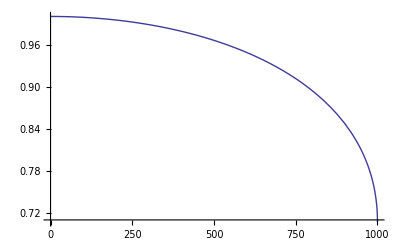

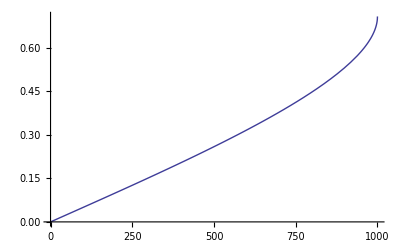

0.785398

```mathematica
delta = 0;
projectileSpeed = 100;
g=-10;
angle = ArcCos[1/(√2)(√((2 delta^2 projectileSpeed^4+distance^2 projectileSpeed^2 (delta g+projectileSpeed^2)+√(distance^4 projectileSpeed^4 (-distance^2 g^2-2 delta g projectileSpeed^2+projectileSpeed^4)))/((delta^2+distance^2) projectileSpeed^4)))];
Cos[angle]
Sin[angle]
Plot[Cos[angle], {distance, 0, 1000}]
Plot[Sin[angle], {distance, 0, 1000}]
N[Pi/4]
```